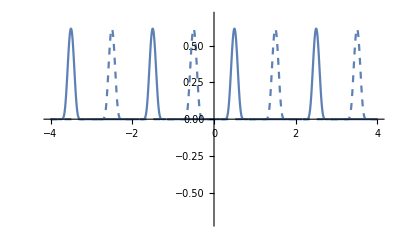

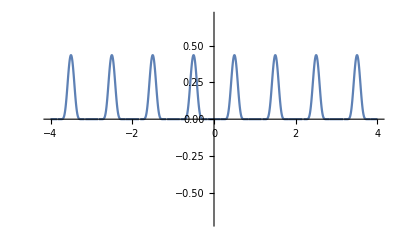

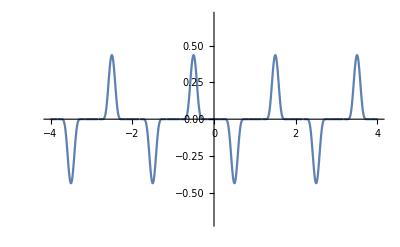

```mathematica
L=1;
NN=4;
phiP[x_]:=Exp[-1/((L/3)^2-(x^2))]HeavisideTheta[-Abs[x]+L/3] 5000
phi[x_] := phiP[x-L/2]
zeroP[x_]:=Sum[phi[x- (2 k  + 1)L],{k,-NN/2,NN/2}]
oneP[x_] := Sum[phi[x-2k L],{k,-NN/2,NN/2}]
plusP[x_]:=(oneP[x] + zeroP[x])/Sqrt[2]
minusP[x_]:=(zeroP[x] - oneP[x])/Sqrt[2]

p1=Plot[zeroP[x],{x,-4,4}, PlotRange->{-0.7,0.7}, PlotStyle->Dashed];
p0=Plot[oneP[x],{x,-4,4}, PlotRange->{-0.7,0.7}];

Show[p0,p1]
Plot[plusP[x],{x,-4,4}, PlotRange->{-0.7,0.7}]
Plot[minusP[x],{x,-4,4}, PlotRange->{-0.7,0.7}]
```